```mathematica
fel[a_]=4a/(a+1)^2;
fin[a_]= a/(a+1)^2;
SetOptions[Plot,BaseStyle->{FontFamily->"Verdana",FontSize->14}];
```

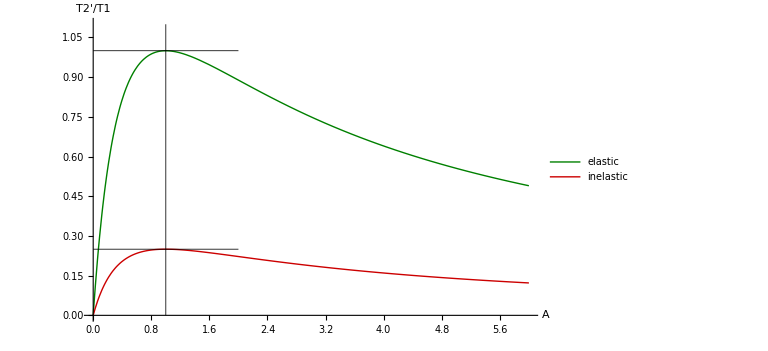

```mathematica
graph = Plot[{fel[A],fin[A]},{A,0,6},PlotStyle->{{Thick,Darker[Green,0.5]},{Thick,Darker[Red,0.2]}},PlotLegends->{"elastic","inelastic"},AxesLabel->{"A","T2'/T1"}];
lines = Graphics[{Thickness[0.001],Line[{{1,0},{1,1.1}}],Line[{{0,1},{2,1}}],Line[{{0,0.25},{2,0.25}}]}];
Show[graph, lines,PlotRange->All]
```